```mathematica
D[r^3*Exp[-r/(2a0)],r]
```

3 ⅇ^(-r/(2 a0)) r^2-(ⅇ^(-r/(2 a0)) r^3)/(2 a0)

```mathematica
Solve[3 ⅇ^(-r/(2 a0)) r^2-(ⅇ^(-r/(2 a0)) r^3)/(2 a0)==0, r]
```

{{r→0},{r→0},{r→6 a0}}

# polar plot of ψ1

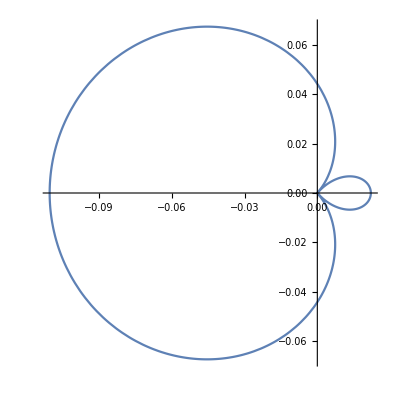

```mathematica
ParametricPlot[{Abs[(1/Sqrt[2])*(Sqrt[Pi/4]*(-4)*Exp[-3]/Sqrt[8]+Sqrt[3Pi/4]*6Cos[t]*Exp[-3]/Sqrt[24])]*Cos[t],Abs[(1/Sqrt[2])*(Sqrt[Pi/4]*(-4)*Exp[-3]/Sqrt[8]+Sqrt[3Pi/4]*6Cos[t]*Exp[-3]/Sqrt[24])]*Sin[t]},{t, 0, 2Pi}]
```

# polar plot of ψ2

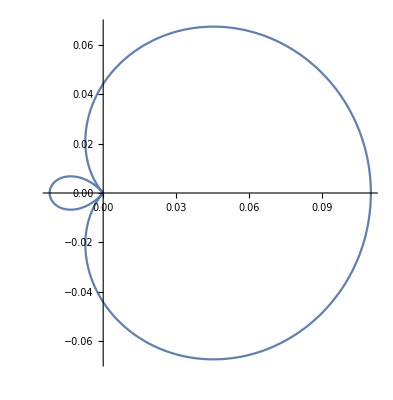

```mathematica
ParametricPlot[{Abs[(1/Sqrt[2])*(Sqrt[Pi/4]*(-4)*Exp[-3]/Sqrt[8]-Sqrt[3Pi/4]*6Cos[t]*Exp[-3]/Sqrt[24])]*Cos[t],Abs[(1/Sqrt[2])*(Sqrt[Pi/4]*(-4)*Exp[-3]/Sqrt[8]-Sqrt[3Pi/4]*6Cos[t]*Exp[-3]/Sqrt[24])]*Sin[t]},{t, 0, 2Pi}]
```

# sp 杂化轨道（2px,2s），ψ1

```mathematica
ContourPlot[1/2 ((√(π/4) ((2-√(x^2+y^2)) Exp[-1/2 √(x^2+y^2)]))/(√8)+(√((3 π)/4) x Exp[-1/2 √(x^2+y^2)])/(2 √6))^2,{x,-9,9},{y,-9,9},PlotTheme->"Detailed",ColorFunction->Hue,MaxRecursion->5,Contours->{0.002,0.004,0.006,0.008,0.01,0.012,0.014,0.016,0.018,0.02,0.022,0.024, 0.026,0.028,0.030,0.032,0.034,0.036,0.038,0.040},PlotRange->0.05]
```

-Graphics-

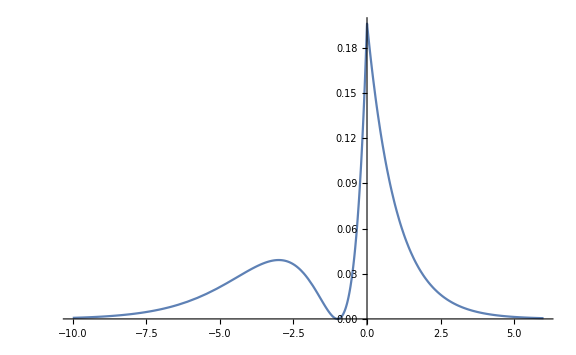

```mathematica
Plot[(1/2)*(Sqrt[1/4Pi](1/Sqrt[8]*(2-Abs[r])*Exp[-Abs[r]/2])+(Sqrt[3/4Pi]*(r)*(1/(2*Sqrt[6]))*Exp[-Abs[r]/2]))^2,{r,-10,6},PlotRange->All, ImageSize->Large]
```

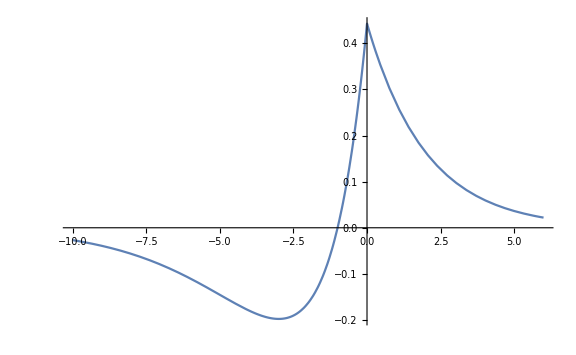

```mathematica
Plot[Sqrt[1/2]*(Sqrt[1/4Pi](1/Sqrt[8]*(2-Abs[r])*Exp[-Abs[r]/2])+(Sqrt[3/4Pi]*(r)*(1/(2*Sqrt[6]))*Exp[-Abs[r]/2])),{r,-10,6},PlotRange->All, ImageSize->Large]
```

```mathematica
ParametricPlot3D[{r Cos[t],r Sin[t],20((√(π/4) ((2-r) Exp[-r/2]))/(√8)+(√((3 π)/4) r Cos[t] Exp[-r/2])/(2 √6))^2},{r,0,10},{t,0,2 π},PlotTheme->"Detailed",Mesh->50,MeshFunctions->{#3&},PlotRange->Full,PlotPoints->25, ImageSize->Large]
```

-Graphics3D-

# ψ2：

```mathematica
ContourPlot[1/2 ((√(π/4) ((2-√(x^2+y^2)) Exp[-1/2 √(x^2+y^2)]))/(√8)-(√((3 π)/4) x Exp[-1/2 √(x^2+y^2)])/(2 √6))^2,{x,-9,9},{y,-9,9},PlotTheme->"Detailed",ColorFunction->Hue,MaxRecursion->5,Contours->{0.002,0.004,0.006,0.008,0.01,0.012,0.014,0.016,0.018,0.02,0.022,0.024, 0.026,0.028,0.030,0.032,0.034,0.036,0.038,0.040},PlotRange->0.05]
```

-Graphics-

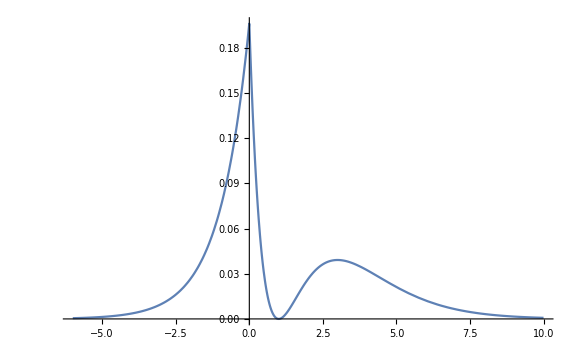

```mathematica
Plot[(1/2)*(Sqrt[1/4Pi](1/Sqrt[8]*(2-Abs[r])*Exp[-Abs[r]/2])-(Sqrt[3/4Pi]*(r)*(1/(2*Sqrt[6]))*Exp[-Abs[r]/2]))^2,{r,-6,10},PlotRange->All, ImageSize->Large]
```

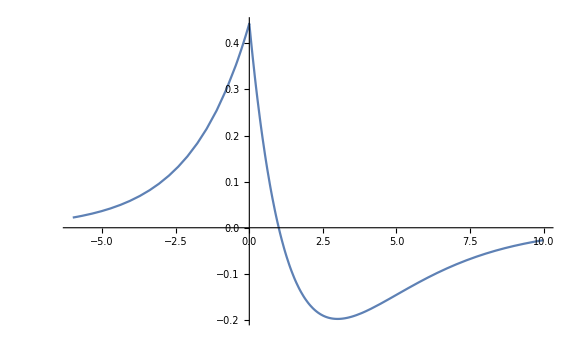

```mathematica
Plot[Sqrt[1/2]*(Sqrt[1/4Pi](1/Sqrt[8]*(2-Abs[r])*Exp[-Abs[r]/2])-(Sqrt[3/4Pi]*(r)*(1/(2*Sqrt[6]))*Exp[-Abs[r]/2])),{r,-6,10},PlotRange->All, ImageSize->Large]
```

```mathematica
ParametricPlot3D[{r Cos[t],r Sin[t],20((√(π/4) ((2-r) Exp[-r/2]))/(√8)-(√((3 π)/4) r Cos[t] Exp[-r/2])/(2 √6))^2},{r,0,10},{t,0,2 π},PlotTheme->"Detailed",Mesh->50,MeshFunctions->{#3&},PlotRange->Full,PlotPoints->25,ImageSize->Large]
```

-Graphics3D-